```mathematica
Soluções de equações
```

Solve [<equacao>, <variavel>]
Solve [ {<eq1>, <eq2>, ..., <eq>}, { <var1>, <var2>, ... ,<var> } ]

```mathematica
Solve[x^2-1==0, x]
```

{{x→-1},{x→1}}

“==” : teste logico
“=”: atribuição

```mathematica
10==10
```

True

```mathematica
10==7
```

False

```mathematica
Solve[{x^2+y^2==2, x-3y==4}, {x, y}]
```

{{x→-1/5,y→-7/5},{x→1,y→-1}}

Há casos, entretanto, que nao se pode resolver de forma analítica, mas apenas de forma númerica, nesses casos utilizamos a função FindRoot.
Exemplo:

```mathematica
eq = Sin[θ]== θ/3
```

Sin[θ]==θ/3

```mathematica
Solve [eq, θ]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[Sin[θ]==θ/3,θ]

Vejamos o grafico:

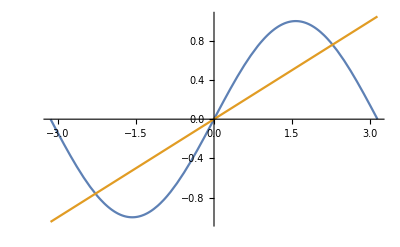

```mathematica
Plot[{Sin[θ], θ/3}, {θ, -π, π}]
```

Como vemos, há solucão, por exemplo em valores proximos de -3, 0, 3
FindRoot[<equacao>, {<variavel>, <valor_prox>}]
precisa receber u valor proximo de uma das solucões da equacao, para obter esse valor por metodos numericos.

```mathematica
FindRoot [ eq, {θ, -2.}]
```

{θ→-2.27886}